```mathematica
Clear["Global`*"]
```

## Rotation matrix

```mathematica
Rx[θ_]:={{Cos[θ],0,-Sin[θ]},{0,1,0},{Sin[θ],0,Cos[θ]}};
Ry[θ_]:={{Cos[θ],-Sin[θ],0},{Sin[θ],Cos[θ],0},{0,0,1}};
Rz[θ_]:={{1,0,0},{0,Cos[θ],-Sin[θ]},{0,Sin[θ],Cos[θ]}};
```

```mathematica
Ry[-π/2]//MatrixForm
```

(0 | 1 | 0
-1 | 0 | 0
0 | 0 | 1)

```mathematica
Ry[θ]//MatrixForm
```

(Cos[θ] | -Sin[θ] | 0
Sin[θ] | Cos[θ] | 0
0 | 0 | 1)

```mathematica
Rz[θ]//MatrixForm
```

(1 | 0 | 0
0 | Cos[θ] | -Sin[θ]
0 | Sin[θ] | Cos[θ])

## Vectors on different panels (cube)

```mathematica
(*x=Tan[α],y=Tan[β],(z,x,y) ordering *)
```

```mathematica
(*panel 1*)
```

```mathematica
vecCube[x_,y_,1]:={1,x,y};
```

```mathematica
vecCube[x,y,1]
```

{1,x,y}

```mathematica
(*panel 2*)
```

```mathematica
vecCube[x_,y_,2]:=Ry[π/2].vecCube[x,y,1]
```

```mathematica
vecCube[x,y,2]
```

{-x,1,y}

```mathematica
(*panel 5*)
```

```mathematica
vecCube[x_,y_,5]:=Ry[π/2].vecCube[x,y,2]
```

```mathematica
vecCube[x,y,5]
```

{-1,-x,y}

```mathematica
(*panel 4*)
```

```mathematica
vecCube[x_,y_,4]:=Rz[π/2].vecCube[x,y,2]
```

```mathematica
vecCube[x,y,4]
```

{-x,-y,1}

```mathematica
(*panel 3*)
```

```mathematica
vecCube[x_,y_,3]:=Rz[-π/2].vecCube[x,y,2]
```

```mathematica
vecCube[x,y,3]
```

{-x,y,-1}

```mathematica
(*panel 6, assuming x points southward *)
```

```mathematica
vecCube[x_,y_,6]:=Rz[π].vecCube[x,y,2]
```

```mathematica
vecCube[x,y,6]
```

{-x,-1,-y}

```mathematica
Table[vecCube[x,y,n],{n,1,6}]//MatrixForm
```

(1 | x | y
-x | 1 | y
-x | y | -1
-x | -y | 1
-1 | -x | y
-x | -1 | -y)

## Vectors on different panels (sphere)

{r/(√(1+x^2+y^2)),(r x)/(√(1+x^2+y^2)),(r y)/(√(1+x^2+y^2))}

```mathematica
(*spherical radius is r*)
```

```mathematica
delta=Sqrt[1+x^2+y^2];
```

```mathematica
vecSphere[r_,x_,y_,n_]:=r*vecCube[x,y,n]/delta;
```

```mathematica
Table[vecSphere[r,x,y,n],{n,1,6}]//Simplify
```

{{r/(√(1+x^2+y^2)),(r x)/(√(1+x^2+y^2)),(r y)/(√(1+x^2+y^2))},{-(r x)/(√(1+x^2+y^2)),r/(√(1+x^2+y^2)),(r y)/(√(1+x^2+y^2))},{-(r x)/(√(1+x^2+y^2)),(r y)/(√(1+x^2+y^2)),-r/(√(1+x^2+y^2))},{-(r x)/(√(1+x^2+y^2)),-(r y)/(√(1+x^2+y^2)),r/(√(1+x^2+y^2))},{-r/(√(1+x^2+y^2)),-(r x)/(√(1+x^2+y^2)),(r y)/(√(1+x^2+y^2))},{-(r x)/(√(1+x^2+y^2)),-r/(√(1+x^2+y^2)),-(r y)/(√(1+x^2+y^2))}}

```mathematica
vecSphere[r,x,y,1].vecSphere[r,x,y,1]//Simplify
```

r^2

```mathematica
vecSphere[r,x,y,1]
```

{r/(√(1+x^2+y^2)),(r x)/(√(1+x^2+y^2)),(r y)/(√(1+x^2+y^2))}

## Basis vectors

```mathematica
(*dxdα=1+x^2,dydβ=1+y^2*)
```

```mathematica
b1[n_]:=D[vecSphere[r,x,y,n],r]//Simplify;
b2[n_]:=FullSimplify[D[vecSphere[r,x,y,n],x]*(1+x^2)/Norm[D[vecSphere[r,x,y,n],x]*(1+x^2)],Assumptions->{x>0,y>0,r>0}];
b3[n_]:=FullSimplify[D[vecSphere[r,x,y,n],y]*(1+y^2)/Norm[D[vecSphere[r,x,y,n],y]*(1+y^2)],Assumptions->{x>0,y>0,r>0}];
(*b2[n_]:=FullSimplify[D[vecSphere[r,x,y,n],x]*(1+x^2),Assumptions->{x>0,y>0,r>0}];
b3[n_]:=FullSimplify[D[vecSphere[r,x,y,n],y]*(1+y^2),Assumptions->{x>0,y>0,r>0}];*)
```

```mathematica
Table[b1[n],{n,1,6}]//MatrixForm
```

(1/(√(1+x^2+y^2)) | x/(√(1+x^2+y^2)) | y/(√(1+x^2+y^2))
-x/(√(1+x^2+y^2)) | 1/(√(1+x^2+y^2)) | y/(√(1+x^2+y^2))
-x/(√(1+x^2+y^2)) | y/(√(1+x^2+y^2)) | -1/(√(1+x^2+y^2))
-x/(√(1+x^2+y^2)) | -y/(√(1+x^2+y^2)) | 1/(√(1+x^2+y^2))
-1/(√(1+x^2+y^2)) | -x/(√(1+x^2+y^2)) | y/(√(1+x^2+y^2))
-x/(√(1+x^2+y^2)) | -1/(√(1+x^2+y^2)) | -y/(√(1+x^2+y^2)))

```mathematica
Table[b2[n],{n,1,6}]//MatrixForm
```

(-x/(√((1+y^2) (1+x^2+y^2))) | √((1+y^2)/(1+x^2+y^2)) | -(x y)/(√((1+y^2) (1+x^2+y^2)))
-√((1+y^2)/(1+x^2+y^2)) | -x/(√((1+y^2) (1+x^2+y^2))) | -(x y)/(√((1+y^2) (1+x^2+y^2)))
-√((1+y^2)/(1+x^2+y^2)) | -(x y)/(√((1+y^2) (1+x^2+y^2))) | x/(√((1+y^2) (1+x^2+y^2)))
-√((1+y^2)/(1+x^2+y^2)) | (x y)/(√((1+y^2) (1+x^2+y^2))) | -x/(√((1+y^2) (1+x^2+y^2)))
x/(√((1+y^2) (1+x^2+y^2))) | -√((1+y^2)/(1+x^2+y^2)) | -(x y)/(√((1+y^2) (1+x^2+y^2)))
-√((1+y^2)/(1+x^2+y^2)) | x/(√((1+y^2) (1+x^2+y^2))) | (x y)/(√((1+y^2) (1+x^2+y^2))))

```mathematica
Table[b3[n],{n,1,6}]//MatrixForm
```

(-y/(√((1+x^2) (1+x^2+y^2))) | -(x y)/(√((1+x^2) (1+x^2+y^2))) | √((1+x^2)/(1+x^2+y^2))
(x y)/(√((1+x^2) (1+x^2+y^2))) | -y/(√((1+x^2) (1+x^2+y^2))) | √((1+x^2)/(1+x^2+y^2))
(x y)/(√((1+x^2) (1+x^2+y^2))) | √((1+x^2)/(1+x^2+y^2)) | y/(√((1+x^2) (1+x^2+y^2)))
(x y)/(√((1+x^2) (1+x^2+y^2))) | -√((1+x^2)/(1+x^2+y^2)) | -y/(√((1+x^2) (1+x^2+y^2)))
y/(√((1+x^2) (1+x^2+y^2))) | (x y)/(√((1+x^2) (1+x^2+y^2))) | √((1+x^2)/(1+x^2+y^2))
(x y)/(√((1+x^2) (1+x^2+y^2))) | y/(√((1+x^2) (1+x^2+y^2))) | -√((1+x^2)/(1+x^2+y^2)))

```mathematica
(* differential length *)
```

```mathematica
delx =Simplify[Norm[D[vecSphere[r,x,y,1],x]*(1+x^2)],Assumptions->{x>0,y>0,r>0}]
```

(r (1+x^2) √(1+y^2))/(1+x^2+y^2)

```mathematica
dely=Simplify[Norm[D[vecSphere[r,x,y,1],y]*(1+y^2)],Assumptions->{x>0,y>0,r>0}]
```

(r √(1+x^2) (1+y^2))/(1+x^2+y^2)

```mathematica
Simplify[b1[1].b2[1],Assumptions->{x∈Reals,y∈Reals,r∈Reals}]
```

0

```mathematica
Simplify[b1[1].b3[1],Assumptions->{x∈Reals,y∈Reals,r∈Reals}]
```

0

```mathematica
Simplify[b2[1].b3[1],Assumptions->{x∈Reals,y∈Reals,r∈Reals}]
```

-(x y)/(√((1+x^2) (1+y^2)))

```mathematica
Simplify[Table[Norm[b1[n]],{n,1,6}],Assumptions->{x>0,y>0,r>0}]
```

{1,1,1,1,1,1}

```mathematica
Simplify[Table[Norm[b2[n]],{n,1,6}],Assumptions->{x>0,y>0,r>0}]
```

{1,1,1,1,1,1}

```mathematica
Simplify[Table[Norm[b3[n]],{n,1,6}],Assumptions->{x>0,y>0,r>0}]
```

{1,1,1,1,1,1}

## Metric tensor

```mathematica
gMat[n_]:=Simplify[{
{b1[n].b1[n],b1[n].b2[n],b1[n].b3[n]},
{b2[n].b1[n],b2[n].b2[n],b2[n].b3[n]},
{b3[n].b1[n],b3[n].b2[n],b3[n].b3[n]}
},Assumptions->{x>0,y>0,r>0}]
```

```mathematica
gMat[2]//MatrixForm
```

(1 | 0 | 0
0 | 1 | -(x y)/(√((1+x^2) (1+y^2)))
0 | -(x y)/(√((1+x^2) (1+y^2))) | 1)

```mathematica
(* metric tensor is the same on every panel*)
```

```mathematica
coMetric=gMat[1]
```

{{1,0,0},{0,1,-(x y)/(√((1+x^2) (1+y^2)))},{0,-(x y)/(√((1+x^2) (1+y^2))),1}}

```mathematica
contraMetric=Inverse[coMetric]//Simplify
```

{{1,0,0},{0,((1+x^2) (1+y^2))/(1+x^2+y^2),(x y √((1+x^2) (1+y^2)))/(1+x^2+y^2)},{0,(x y √((1+x^2) (1+y^2)))/(1+x^2+y^2),((1+x^2) (1+y^2))/(1+x^2+y^2)}}

```mathematica
contraMetric//MatrixForm
```

(1 | 0 | 0
0 | ((1+x^2) (1+y^2))/(1+x^2+y^2) | (x y √((1+x^2) (1+y^2)))/(1+x^2+y^2)
0 | (x y √((1+x^2) (1+y^2)))/(1+x^2+y^2) | ((1+x^2) (1+y^2))/(1+x^2+y^2))

```mathematica
Simplify[Sqrt[Det[coMetric]],Assumptions->{r>0,x>0,y>0}]
```

√((1+x^2+y^2)/((1+x^2) (1+y^2)))

```mathematica
sqrtG=Simplify[Sqrt[Det[coMetric]],Assumptions->{r>0,x>0,y>0}]
```

√((1+x^2+y^2)/((1+x^2) (1+y^2)))

```mathematica
coMetricXY=Table[coMetric⟦i,j⟧,{i,2,3},{j,2,3}]
```

{{1,-(x y)/(√((1+x^2) (1+y^2)))},{-(x y)/(√((1+x^2) (1+y^2))),1}}

```mathematica
gfac=(r^2 (1+x^2) (1+y^2))/((1+x^2+y^2)^2)
```

(r^2 (1+x^2) (1+y^2))/((1+x^2+y^2)^2)

```mathematica
coMetricXY/gfac//MatrixForm
```

(((1+x^2+y^2)^2)/(r^2 (1+x^2) (1+y^2)) | -(x y (1+x^2+y^2)^2)/(r^2 (1+x^2) (1+y^2) √((1+x^2) (1+y^2)))
-(x y (1+x^2+y^2)^2)/(r^2 (1+x^2) (1+y^2) √((1+x^2) (1+y^2))) | ((1+x^2+y^2)^2)/(r^2 (1+x^2) (1+y^2)))

## Christoffel symbols

```mathematica
symbols={r,x,y};
coFactor={1,(1+x^2)/delx,(1+y^2)/dely};
(*coFactor={1,(1+x^2),(1+y^2)};*)
```

```mathematica
(* covariant basis vector is a column vector *)
```

```mathematica
coBasis[n_]:=Transpose[{b1[n],b2[n],b3[n]}];
```

```mathematica
coBasis[1]//MatrixForm
```

(1/(√(1+x^2+y^2)) | -x/(√((1+y^2) (1+x^2+y^2))) | -y/(√((1+x^2) (1+x^2+y^2)))
x/(√(1+x^2+y^2)) | √((1+y^2)/(1+x^2+y^2)) | -(x y)/(√((1+x^2) (1+x^2+y^2)))
y/(√(1+x^2+y^2)) | -(x y)/(√((1+y^2) (1+x^2+y^2))) | √((1+x^2)/(1+x^2+y^2)))

```mathematica
b1[1]
```

{1/(√(1+x^2+y^2)),x/(√(1+x^2+y^2)),y/(√(1+x^2+y^2))}

```mathematica
(* contravaraince basis vector is a row vector *)
```

```mathematica
contraBasis[n_]:=Simplify[Table[
Sum[contraMetric[[i,k]]*coBasis[n][[All,k]],{k,1,3}],
{i,1,3}],Assumptions->{x>0,y>0,r>0}]
```

```mathematica
contraBasis[1]//MatrixForm
```

(1/(√(1+x^2+y^2)) | x/(√(1+x^2+y^2)) | y/(√(1+x^2+y^2))
-x √((1+y^2)/(1+x^2+y^2)) | √((1+y^2)/(1+x^2+y^2)) | 0
-y √((1+x^2)/(1+x^2+y^2)) | 0 | √((1+x^2)/(1+x^2+y^2)))

```mathematica
contraBasis[2]//MatrixForm
```

(-x/(√(1+x^2+y^2)) | 1/(√(1+x^2+y^2)) | y/(√(1+x^2+y^2))
-√((1+y^2)/(1+x^2+y^2)) | -x √((1+y^2)/(1+x^2+y^2)) | 0
0 | -y √((1+x^2)/(1+x^2+y^2)) | √((1+x^2)/(1+x^2+y^2)))

```mathematica
FullSimplify[contraBasis[1]⟦2⟧.b3[1],Assumptions->{x>0,y>0,r>0}]
```

0

```mathematica
Simplify[contraBasis[1].coBasis[1],Assumptions->{x>0,y>0,r>0}]//MatrixForm
```

(1 | 0 | 0
0 | 1 | 0
0 | 0 | 1)

```mathematica
Simplify[contraBasis[2].coBasis[2],Assumptions->{x>0,y>0,r>0}]//MatrixForm
```

(1 | 0 | 0
0 | 1 | 0
0 | 0 | 1)

```mathematica
D[coBasis[1][[All,1]],symbols[[3]]]//Simplify
```

{-y/((1+x^2+y^2)^(3/2)),-(x y)/((1+x^2+y^2)^(3/2)),(1+x^2)/((1+x^2+y^2)^(3/2))}

```mathematica
%.coFactor
```

-y/((1+x^2+y^2)^(3/2))+(√(1+x^2))/(r √(1+x^2+y^2))-(x y)/(r √(1+y^2) √(1+x^2+y^2))

```mathematica
D[coBasis[2,1],symbols⟦2⟧]
```

0

```mathematica
contraBasis[2][[1]]
```

{-x/(√(1+x^2+y^2)),1/(√(1+x^2+y^2)),y/(√(1+x^2+y^2))}

```mathematica
Christoffel[i_,j_,k_,n_]:=(D[coBasis[n][[All,j]],symbols[[k]]]*coFactor[[k]]).(contraBasis[n][[i,All]])
```

```mathematica
Christoffel[i_,j_,k_]:=Sum[1/2*contraMetric⟦i,m⟧*
(D[coMetric⟦m,i⟧,symbols[[j]]]*coFactor[[j]]
+D[coMetric[[m,j]],symbols[[i]]]*coFactor[[i]]
-D[coMetric[[i,j]],symbols[[m]]]*coFactor[[m]]),{m,1,3}];
```

```mathematica
FullSimplify[Table[Christoffel[1,j,k],{j,1,3},{k,1,3}],Assumptions->{x>0,y>0,r>0}]//MatrixForm
```

(0 | 0 | 0
0 | 0 | 0
0 | 0 | 0)

```mathematica
FullSimplify[Table[Christoffel[1,j,k,1],{j,1,3},{k,1,3}],Assumptions->{x>0,y>0,r>0}]//MatrixForm
```

(0 | 0 | 0
0 | -1/r | (x y)/(r √((1+x^2) (1+y^2)))
0 | (x y)/(r √((1+x^2) (1+y^2))) | -1/r)

```mathematica
FullSimplify[Table[Christoffel[2,j,k,1],{j,1,3},{k,1,3}],Assumptions->{x>0,y>0,r>0}]//MatrixForm
```

(0 | 1/r | 0
0 | 0 | -(x^2 y)/(√(1+x^2) (r+r y^2))
0 | -y/(r √(1+x^2)) | 0)

```mathematica
FullSimplify[Table[Christoffel[3,j,k,1],{j,1,3},{k,1,3}],Assumptions->{x>0,y>0,r>0}]//MatrixForm
```

(0 | 0 | 1/r
0 | 0 | -x/(r √(1+y^2))
0 | -(x y^2)/((r+r x^2) √(1+y^2)) | 0)

```mathematica
(* Christoffel symbol can be defined by the metric tensor, so it should not depend on panels, using panel=1*)
```

```mathematica
gammaCh[i_]:=FullSimplify[Table[Christoffel[i,j,k,1],{j,1,3},{k,1,3}],Assumptions->{x>0,y>0,r>0}]
```

```mathematica
gammaCh[1]
```

{{0,0,0},{0,-1/r,(x y)/(r √((1+x^2) (1+y^2)))},{0,(x y)/(r √((1+x^2) (1+y^2))),-1/r}}

```mathematica
gammaCh[1]//MatrixForm
```

(0 | 0 | 0
0 | -1/r | (x y)/(r √((1+x^2) (1+y^2)))
0 | (x y)/(r √((1+x^2) (1+y^2))) | -1/r)

```mathematica
gammaCh[2]//MatrixForm
```

(0 | 1/r | 0
0 | 0 | -(x^2 y)/(√(1+x^2) (r+r y^2))
0 | -y/(r √(1+x^2)) | 0)

```mathematica
gammaCh[3]//MatrixForm
```

(0 | 0 | 1/r
0 | 0 | -x/(r √(1+y^2))
0 | -(x y^2)/((r+r x^2) √(1+y^2)) | 0)

```mathematica
FullSimplify[Table[Tr[gammaCh[i].contraMetric],{i,1,3}],Assumptions->{x>0,y>0,r>0}]
```

{-2/r,-(x y^2)/(r √(1+y^2)),-(x^2 y)/(r √(1+x^2))}

## Metric terms (momentum)

```mathematica
SS=Superscript
```

Superscript

```mathematica
SS[v,1]
```

v^1

```mathematica
lengths={1,delx,dely}
```

{1,(r (1+x^2) √(1+y^2))/(1+x^2+y^2),(r √(1+x^2) (1+y^2))/(1+x^2+y^2)}

```mathematica
FluxTensor=Table[ρ*SS[v,i]*SS[v,j],{i,1,3},{j,1,3}]+contraMetric*p
```

{{p+ρ (v^1)^2,ρ v^1 v^2,ρ v^1 v^3},{ρ v^1 v^2,(p (1+x^2) (1+y^2))/(1+x^2+y^2)+ρ (v^2)^2,(p x y √((1+x^2) (1+y^2)))/(1+x^2+y^2)+ρ v^2 v^3},{ρ v^1 v^3,(p x y √((1+x^2) (1+y^2)))/(1+x^2+y^2)+ρ v^2 v^3,(p (1+x^2) (1+y^2))/(1+x^2+y^2)+ρ (v^3)^2}}

```mathematica
FluxTensor//Simplify//MatrixForm
```

(p+ρ (v^1)^2 | ρ v^1 v^2 | ρ v^1 v^3
ρ v^1 v^2 | (p (1+x^2) (1+y^2))/(1+x^2+y^2)+ρ (v^2)^2 | (p x y √((1+x^2) (1+y^2)))/(1+x^2+y^2)+ρ v^2 v^3
ρ v^1 v^3 | (p x y √((1+x^2) (1+y^2)))/(1+x^2+y^2)+ρ v^2 v^3 | (p (1+x^2) (1+y^2))/(1+x^2+y^2)+ρ (v^3)^2)

```mathematica
Simplify[Sum[gammaCh[3]⟦i,j⟧*contraMetric⟦i,j⟧,{i,2,3},{j,2,3}],Assumptions->{x>0,y>0,r>0}]
```

-(x^2 y)/(r √(1+x^2))

```mathematica
FullSimplify[gammaCh[1].FluxTensor,Assumptions->{x>0,y>0,r>0}]//MatrixForm
```

(0 | 0 | 0
(ρ v^1 (-v^2+(x y v^3)/(√((1+x^2) (1+y^2)))))/r | -(p+ρ v^2 (v^2-(x y v^3)/(√((1+x^2) (1+y^2)))))/r | (ρ v^3 (-v^2+(x y v^3)/(√((1+x^2) (1+y^2)))))/r
(ρ v^1 ((x y v^2)/(√((1+x^2) (1+y^2)))-v^3))/r | (ρ v^2 ((x y v^2)/(√((1+x^2) (1+y^2)))-v^3))/r | -(p+ρ v^3 (-(x y v^2)/(√((1+x^2) (1+y^2)))+v^3))/r)

```mathematica
FullSimplify[Tr[gammaCh[1].FluxTensor],Assumptions->{x>0,y>0,r>0}]
```

-(2 p+ρ ((v^2)^2-(2 x y v^2 v^3)/(√((1+x^2) (1+y^2)))+(v^3)^2))/r

```mathematica
FullSimplify[Tr[gammaCh[2].FluxTensor],Assumptions->{x>0,y>0,r>0}]
```

(-(p x y^2)/(√(1+y^2))+ρ v^2 (v^1-(y (1+x^2+y^2) v^3)/(√(1+x^2) (1+y^2))))/r

```mathematica
FullSimplify[Tr[gammaCh[3].FluxTensor],Assumptions->{x>0,y>0,r>0}]
```

(-(p x^2 y)/(√(1+x^2))+ρ (v^1-(x (1+x^2+y^2) v^2)/((1+x^2) √(1+y^2))) v^3)/r

## Metric terms (flux form)

```mathematica
SS=Superscript
```

Superscript

```mathematica
SS[v,1]
```

v^1

```mathematica
lengths={1,delx,dely}
```

{1,(r (1+x^2) √(1+y^2))/(1+x^2+y^2),(r √(1+x^2) (1+y^2))/(1+x^2+y^2)}

```mathematica
FluxTensor=Table[{SS[F,i],SS[G,i],SS[H,i]},{i,1,3}]
```

{{F^1,G^1,H^1},{F^2,G^2,H^2},{F^3,G^3,H^3}}

```mathematica
FullSimplify[gammaCh[1].FluxTensor,Assumptions->{x>0,y>0,r>0}]//MatrixForm
```

(0 | 0 | 0
(-F^2+(x y F^3)/(√((1+x^2) (1+y^2))))/r | (-G^2+(x y G^3)/(√((1+x^2) (1+y^2))))/r | (-H^2+(x y H^3)/(√((1+x^2) (1+y^2))))/r
((x y F^2)/(√((1+x^2) (1+y^2)))-F^3)/r | ((x y G^2)/(√((1+x^2) (1+y^2)))-G^3)/r | ((x y H^2)/(√((1+x^2) (1+y^2)))-H^3)/r)

```mathematica
FullSimplify[Tr[gammaCh[1].FluxTensor],Assumptions->{x>0,y>0,r>0}]
```

-(G^2-(x y (G^3+H^2))/(√((1+x^2) (1+y^2)))+H^3)/r

```mathematica
FullSimplify[Tr[gammaCh[2].FluxTensor],Assumptions->{x>0,y>0,r>0}]
```

(F^2-(y (x^2 G^3+(1+y^2) H^2))/(√(1+x^2) (1+y^2)))/r

```mathematica
FullSimplify[Tr[gammaCh[3].FluxTensor],Assumptions->{x>0,y>0,r>0}]
```

(F^3-(x ((1+x^2) G^3+y^2 H^2))/((1+x^2) √(1+y^2)))/r

## Metric terms (shallow water)

```mathematica
FluxTensor=Table[h*SS[v,i]*SS[v,j],{i,1,3},{j,1,3}]+contraMetric*(g*h^2/2)
```

{{(g h^2)/2+h (v^1)^2,h v^1 v^2,h v^1 v^3},{h v^1 v^2,(g h^2 (1+x^2) (1+y^2))/(2 (1+x^2+y^2))+h (v^2)^2,(g h^2 x y √((1+x^2) (1+y^2)))/(2 (1+x^2+y^2))+h v^2 v^3},{h v^1 v^3,(g h^2 x y √((1+x^2) (1+y^2)))/(2 (1+x^2+y^2))+h v^2 v^3,(g h^2 (1+x^2) (1+y^2))/(2 (1+x^2+y^2))+h (v^3)^2}}

```mathematica
FluxTensor//Simplify//MatrixForm
```

(1/2 h (g h+2 (v^1)^2) | h v^1 v^2 | h v^1 v^3
h v^1 v^2 | (g h^2 (1+x^2) (1+y^2))/(2 (1+x^2+y^2))+h (v^2)^2 | (g h^2 x y √((1+x^2) (1+y^2)))/(2 (1+x^2+y^2))+h v^2 v^3
h v^1 v^3 | (g h^2 x y √((1+x^2) (1+y^2)))/(2 (1+x^2+y^2))+h v^2 v^3 | (g h^2 (1+x^2) (1+y^2))/(2 (1+x^2+y^2))+h (v^3)^2)

```mathematica
Simplify[Sum[gammaCh[3]⟦i,j⟧*contraMetric⟦i,j⟧,{i,2,3},{j,2,3}],Assumptions->{x>0,y>0,r>0}]
```

-(x^2 y)/(r √(1+x^2))

```mathematica
FullSimplify[Tr[gammaCh[2].FluxTensor],Assumptions->{x>0,y>0,r>0}]
```

(h (-(g h x y^2)/(√(1+y^2))+2 v^2 (v^1-(y (1+x^2+y^2) v^3)/(√(1+x^2) (1+y^2)))))/(2 r)

```mathematica
FullSimplify[Tr[gammaCh[3].FluxTensor],Assumptions->{x>0,y>0,r>0}]
```

(h (-(g h x^2 y)/(√(1+x^2))+2 (v^1-(x (1+x^2+y^2) v^2)/((1+x^2) √(1+y^2))) v^3))/(2 r)

## Finite volume (length, area, volume)

```mathematica
Simplify[Norm[D[vecSphere[r,x,y,1],x]*(1+x^2)],Assumptions->{r>0,x>0,y>0}]
```

(r (1+x^2) √(1+y^2))/(1+x^2+y^2)

```mathematica
Simplify[Norm[D[vecSphere[r,x,y,1],y]*(1+y^2)],Assumptions->{r>0,x>0,y>0}]
```

(r √(1+x^2) (1+y^2))/(1+x^2+y^2)

```mathematica
Simplify[Norm[D[vecSphere[r,x,y,1],r]],Assumptions->{r>0,x>0,y>0}]
```

1

```mathematica
Simplify[Norm[b2[1]],Assumptions->{r>0,x>0,y>0}]
```

1

```mathematica
(* edge length, angular resolution is delA, vertical resolution is delH*)
```

```mathematica
delZ=Simplify[Norm[b1[1]],Assumptions->{r>0,x>0,y>0}]*δH
delX=Simplify[Norm[b2[1]],Assumptions->{r>0,x>0,y>0}]*δA
delY=Simplify[Norm[b3[1]],Assumptions->{r>0,x>0,y>0}]*δA
```

δH

δA

δA

```mathematica
del1=delZ;
del2=delX;
del3=delY;
```

```mathematica
(* angle between covariant basis vectors *)
```

```mathematica
b1[1].b2[1]/Norm[b2[1]]//Simplify
```

-(x (1+y^2-√((1+y^2)/(1+x^2+y^2)) √((1+y^2) (1+x^2+y^2))))/(√(1+x^2+y^2) √((1+y^2) (1+x^2+y^2) (Abs[(1+y^2)/(1+x^2+y^2)]+Abs[x/(√((1+y^2) (1+x^2+y^2)))]^2+Abs[(x y)/(√((1+y^2) (1+x^2+y^2)))]^2)))

```mathematica
b1[1].b3[1]/Norm[b3[1]]//Simplify
```

-(y (1+x^2-√((1+x^2)/(1+x^2+y^2)) √((1+x^2) (1+x^2+y^2))))/(√(1+x^2+y^2) √((1+x^2) (1+x^2+y^2) (Abs[(1+x^2)/(1+x^2+y^2)]+Abs[y/(√((1+x^2) (1+x^2+y^2)))]^2+Abs[(x y)/(√((1+x^2) (1+x^2+y^2)))]^2)))

```mathematica
cosA=Simplify[b2[1].b3[1]/(Norm[b2[1]]*Norm[b3[1]]),Assumptions->{x>0,y>0,r>0}]
```

-(x y)/(√((1+x^2) (1+y^2)))

```mathematica
sinA=Sqrt[1-cosA*cosA]//Simplify
```

√((1+x^2+y^2)/((1+x^2) (1+y^2)))

```mathematica
(* area *)
```

```mathematica
area12=delZ*delX
area13=delZ*delY
area23=Simplify[delX*delY*sinA,Assumptions->{r>0,x>0,y>0}]
```

δA δH

δA δH

√((1+x^2+y^2)/((1+x^2) (1+y^2))) δA^2

```mathematica
(* volume *)
```

```mathematica
vol123=Simplify[delX*delY*delZ*sinA,Assumptions->{r>0,x>0,y>0}]
```

√((1+x^2+y^2)/((1+x^2) (1+y^2))) δA^2 δH

```mathematica
sqrtG
```

√((1+x^2+y^2)/((1+x^2) (1+y^2)))

```mathematica
vol123/sqrtG
```

δA^2 δH

```mathematica
vol123/(area12*del3)
```

√((1+x^2+y^2)/((1+x^2) (1+y^2)))

```mathematica
vol123/(area13*del2)
```

√((1+x^2+y^2)/((1+x^2) (1+y^2)))

```mathematica
vol123/(area23*del1)
```

1

## Coriolis force

```mathematica
(* north panel, n=1 *)
omega={Ω,0,0};
b1[1]
b2[1]
b3[1]
```

{1/(√(1+x^2+y^2)),x/(√(1+x^2+y^2)),y/(√(1+x^2+y^2))}

{-x/(√((1+y^2) (1+x^2+y^2))),√((1+y^2)/(1+x^2+y^2)),-(x y)/(√((1+y^2) (1+x^2+y^2)))}

{-y/(√((1+x^2) (1+x^2+y^2))),-(x y)/(√((1+x^2) (1+x^2+y^2))),√((1+x^2)/(1+x^2+y^2))}

```mathematica
omegaCovariant[n_]:=Table[omega.contraBasis[n]⟦i⟧,{i,1,3}]//Simplify
```

```mathematica
Table[omegaCovariant[i],{i,1,6}]//MatrixForm
```

(Ω/(√(1+x^2+y^2)) | -x √((1+y^2)/(1+x^2+y^2)) Ω | -y √((1+x^2)/(1+x^2+y^2)) Ω
-(x Ω)/(√(1+x^2+y^2)) | -√((1+y^2)/(1+x^2+y^2)) Ω | 0
-(x Ω)/(√(1+x^2+y^2)) | -√((1+y^2)/(1+x^2+y^2)) Ω | 0
-(x Ω)/(√(1+x^2+y^2)) | -√((1+y^2)/(1+x^2+y^2)) Ω | 0
-Ω/(√(1+x^2+y^2)) | x √((1+y^2)/(1+x^2+y^2)) Ω | y √((1+x^2)/(1+x^2+y^2)) Ω
-(x Ω)/(√(1+x^2+y^2)) | -√((1+y^2)/(1+x^2+y^2)) Ω | 0)

```mathematica
(*ϵ^ijk=e^ijk/Sqrt[g]*)
```

```mathematica
epsilon=FullSimplify[Normal[LeviCivitaTensor[3]]/sqrtG,Assumptions->{x>0,y>0}]
```

{{{0,0,0},{0,0,√(((1+x^2) (1+y^2))/(1+x^2+y^2))},{0,-√(((1+x^2) (1+y^2))/(1+x^2+y^2)),0}},{{0,0,-√(((1+x^2) (1+y^2))/(1+x^2+y^2))},{0,0,0},{√(((1+x^2) (1+y^2))/(1+x^2+y^2)),0,0}},{{0,√(((1+x^2) (1+y^2))/(1+x^2+y^2)),0},{-√(((1+x^2) (1+y^2))/(1+x^2+y^2)),0,0},{0,0,0}}}

```mathematica
omegaMatrix[n_]:=Table[
Sum[epsilon[[i,j,k]]*omegaCovariant[n][[j]]*coMetric[[k,l]],{j,1,3},{k,1,3}],
{i,1,3},{l,1,3}];
```

```mathematica
Coriolis1=FullSimplify[omegaMatrix[1],Assumptions->{x>0,y>0}]
```

{{0,((1+2 x^2) y √(1+y^2) Ω)/(1+x^2+y^2),-(x √(1+x^2) (1+2 y^2) Ω)/(1+x^2+y^2)},{-((1+x^2) y √(1+y^2) Ω)/(1+x^2+y^2),(x y Ω)/(1+x^2+y^2),-(√((1+x^2) (1+y^2)) Ω)/(1+x^2+y^2)},{(x √(1+x^2) (1+y^2) Ω)/(1+x^2+y^2),(√((1+x^2) (1+y^2)) Ω)/(1+x^2+y^2),-(x y Ω)/(1+x^2+y^2)}}

```mathematica
Coriolis1//MatrixForm
```

(0 | ((1+2 x^2) y √(1+y^2) Ω)/(1+x^2+y^2) | -(x √(1+x^2) (1+2 y^2) Ω)/(1+x^2+y^2)
-((1+x^2) y √(1+y^2) Ω)/(1+x^2+y^2) | (x y Ω)/(1+x^2+y^2) | -(√((1+x^2) (1+y^2)) Ω)/(1+x^2+y^2)
(x √(1+x^2) (1+y^2) Ω)/(1+x^2+y^2) | (√((1+x^2) (1+y^2)) Ω)/(1+x^2+y^2) | -(x y Ω)/(1+x^2+y^2))

```mathematica
Coriolis2=FullSimplify[omegaMatrix[2],Assumptions->{x>0,y>0}]
```

{{0,(x y √(1+y^2) Ω)/(1+x^2+y^2),-(√(1+x^2) (1+y^2) Ω)/(1+x^2+y^2)},{0,-(x^2 y Ω)/(1+x^2+y^2),(x √((1+x^2) (1+y^2)) Ω)/(1+x^2+y^2)},{(√(1+x^2) (1+y^2) Ω)/(1+x^2+y^2),-(x √((1+x^2) (1+y^2)) Ω)/(1+x^2+y^2),(x^2 y Ω)/(1+x^2+y^2)}}

```mathematica
Coriolis2//MatrixForm
```

(0 | (x y √(1+y^2) Ω)/(1+x^2+y^2) | -(√(1+x^2) (1+y^2) Ω)/(1+x^2+y^2)
0 | -(x^2 y Ω)/(1+x^2+y^2) | (x √((1+x^2) (1+y^2)) Ω)/(1+x^2+y^2)
(√(1+x^2) (1+y^2) Ω)/(1+x^2+y^2) | -(x √((1+x^2) (1+y^2)) Ω)/(1+x^2+y^2) | (x^2 y Ω)/(1+x^2+y^2))

```mathematica
FullSimplify[omegaMatrix[3],Assumptions->{x>0,y>0}]//MatrixForm
```

(0 | (x y √(1+y^2) Ω)/(1+x^2+y^2) | -(√(1+x^2) (1+y^2) Ω)/(1+x^2+y^2)
0 | -(x^2 y Ω)/(1+x^2+y^2) | (x √((1+x^2) (1+y^2)) Ω)/(1+x^2+y^2)
(√(1+x^2) (1+y^2) Ω)/(1+x^2+y^2) | -(x √((1+x^2) (1+y^2)) Ω)/(1+x^2+y^2) | (x^2 y Ω)/(1+x^2+y^2))

```mathematica
FullSimplify[omegaMatrix[4],Assumptions->{x>0,y>0}]//MatrixForm
```

(0 | (x y √(1+y^2) Ω)/(1+x^2+y^2) | -(√(1+x^2) (1+y^2) Ω)/(1+x^2+y^2)
0 | -(x^2 y Ω)/(1+x^2+y^2) | (x √((1+x^2) (1+y^2)) Ω)/(1+x^2+y^2)
(√(1+x^2) (1+y^2) Ω)/(1+x^2+y^2) | -(x √((1+x^2) (1+y^2)) Ω)/(1+x^2+y^2) | (x^2 y Ω)/(1+x^2+y^2))

```mathematica
Coriolis3=FullSimplify[omegaMatrix[5],Assumptions->{x>0,y>0}]
```

{{0,-((1+2 x^2) y √(1+y^2) Ω)/(1+x^2+y^2),(x √(1+x^2) (1+2 y^2) Ω)/(1+x^2+y^2)},{((1+x^2) y √(1+y^2) Ω)/(1+x^2+y^2),-(x y Ω)/(1+x^2+y^2),(√((1+x^2) (1+y^2)) Ω)/(1+x^2+y^2)},{-(x √(1+x^2) (1+y^2) Ω)/(1+x^2+y^2),-(√((1+x^2) (1+y^2)) Ω)/(1+x^2+y^2),(x y Ω)/(1+x^2+y^2)}}

```mathematica
Coriolis3//MatrixForm
```

(0 | -((1+2 x^2) y √(1+y^2) Ω)/(1+x^2+y^2) | (x √(1+x^2) (1+2 y^2) Ω)/(1+x^2+y^2)
((1+x^2) y √(1+y^2) Ω)/(1+x^2+y^2) | -(x y Ω)/(1+x^2+y^2) | (√((1+x^2) (1+y^2)) Ω)/(1+x^2+y^2)
-(x √(1+x^2) (1+y^2) Ω)/(1+x^2+y^2) | -(√((1+x^2) (1+y^2)) Ω)/(1+x^2+y^2) | (x y Ω)/(1+x^2+y^2))

```mathematica
FullSimplify[omegaMatrix[6],Assumptions->{x>0,y>0}]//MatrixForm
```

(0 | (x y √(1+y^2) Ω)/(1+x^2+y^2) | -(√(1+x^2) (1+y^2) Ω)/(1+x^2+y^2)
0 | -(x^2 y Ω)/(1+x^2+y^2) | (x √((1+x^2) (1+y^2)) Ω)/(1+x^2+y^2)
(√(1+x^2) (1+y^2) Ω)/(1+x^2+y^2) | -(x √((1+x^2) (1+y^2)) Ω)/(1+x^2+y^2) | (x^2 y Ω)/(1+x^2+y^2))

```mathematica
omegaMatrix[1]+omegaMatrix[5]//MatrixForm
```

(0 | 0 | 0
0 | 0 | 0
0 | 0 | 0)

```mathematica
omegaMatrix[2]-omegaMatrix[6]
```

{{0,0,0},{0,0,0},{0,0,0}}

```mathematica
Coriolis1.{v1,v2,v3}//Simplify
```

{((v2 (1+2 x^2) y √(1+y^2)-v3 x √(1+x^2) (1+2 y^2)) Ω)/(1+x^2+y^2),((v2 x y-v1 (1+x^2) y √(1+y^2)-v3 √((1+x^2) (1+y^2))) Ω)/(1+x^2+y^2),((-v3 x y+v1 x √(1+x^2) (1+y^2)+v2 √((1+x^2) (1+y^2))) Ω)/(1+x^2+y^2)}

## Ghost zone Interpolation

```mathematica
dA=π/16;
num=π/2/dA+1;
```

```mathematica
corners=Table[-π/4+dA*n,{n,0,num-1}]
```

{-π/4,-(3 π)/16,-π/8,-π/16,0,π/16,π/8,(3 π)/16,π/4}

```mathematica
centers=Table[(corners[[i]]+corners[[i+1]])/2,{i,1,num-1}]
```

{-(7 π)/32,-(5 π)/32,-(3 π)/32,-π/32,π/32,(3 π)/32,(5 π)/32,(7 π)/32}

```mathematica
xcorners=Tan[corners]//N
```

{-1.,-0.668179,-0.414214,-0.198912,0.,0.198912,0.414214,0.668179,1.}

```mathematica
ycorners=Tan[corners]//N
```

{-1.,-0.668179,-0.414214,-0.198912,0.,0.198912,0.414214,0.668179,1.}

```mathematica
xcenters=Tan[centers]//N
```

{-0.820679,-0.534511,-0.303347,-0.0984914,0.0984914,0.303347,0.534511,0.820679}

```mathematica
ycenters=Tan[centers]//N
```

{-0.820679,-0.534511,-0.303347,-0.0984914,0.0984914,0.303347,0.534511,0.820679}

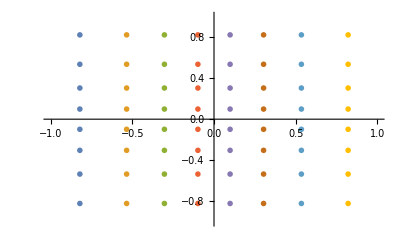
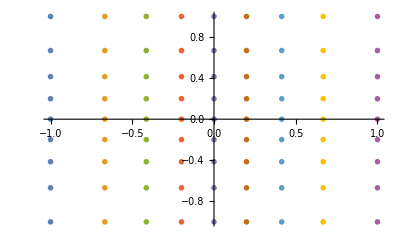

```mathematica
Overlay[{
ListPlot[Outer[List,xcenters,ycenters],PlotMarkers->o,PlotRange->{{-1,1},{-1,1}}],
ListPlot[Outer[List,xcorners,ycorners],PlotMarkers->s,PlotRange->{{-1,1},{-1,1}}]
}]
```

```mathematica
(* ghost cells of pangel 2 *)
```

```mathematica
angles[k_,num_,p_]:=Module[{yghost,dA,corners,centers,baseVec,centerVec,xcenters},
dA=π/(2*num);
corners=Table[-π/4+dA*n,{n,0,num}];
centers=Table[(corners[[i]]+corners[[i+1]])/2,{i,1,num}];
yghost=Tan[centers[[1]]+k*dA];
baseVec=vecCube[0,yghost,p];
xcenters=Tan[centers];
centerVec=Table[vecCube[x,yghost,p],{x,xcenters}];
ArcCos[Table[x.baseVec/(Norm[x]*Norm[baseVec]),{x,centerVec}]]
]
```

```mathematica
angles[0,8,2]
```

{ArcCos[√((1+Tan[(7 π)/32]^2)/(1+2 Tan[(7 π)/32]^2))],ArcCos[√((1+Tan[(7 π)/32]^2)/(1+Tan[(5 π)/32]^2+Tan[(7 π)/32]^2))],ArcCos[√((1+Tan[(7 π)/32]^2)/(1+Tan[(3 π)/32]^2+Tan[(7 π)/32]^2))],ArcCos[√((1+Tan[(7 π)/32]^2)/(1+Tan[π/32]^2+Tan[(7 π)/32]^2))],ArcCos[√((1+Tan[(7 π)/32]^2)/(1+Tan[π/32]^2+Tan[(7 π)/32]^2))],ArcCos[√((1+Tan[(7 π)/32]^2)/(1+Tan[(3 π)/32]^2+Tan[(7 π)/32]^2))],ArcCos[√((1+Tan[(7 π)/32]^2)/(1+Tan[(5 π)/32]^2+Tan[(7 π)/32]^2))],ArcCos[√((1+Tan[(7 π)/32]^2)/(1+2 Tan[(7 π)/32]^2))]}

```mathematica
(* internal cells of pangel 3 *)
```

```mathematica
angles[7,8,3]
```

{ArcCos[√((1+Tan[(7 π)/32]^2)/(1+2 Tan[(7 π)/32]^2))],ArcCos[√((1+Tan[(7 π)/32]^2)/(1+Tan[(5 π)/32]^2+Tan[(7 π)/32]^2))],ArcCos[√((1+Tan[(7 π)/32]^2)/(1+Tan[(3 π)/32]^2+Tan[(7 π)/32]^2))],ArcCos[√((1+Tan[(7 π)/32]^2)/(1+Tan[π/32]^2+Tan[(7 π)/32]^2))],ArcCos[√((1+Tan[(7 π)/32]^2)/(1+Tan[π/32]^2+Tan[(7 π)/32]^2))],ArcCos[√((1+Tan[(7 π)/32]^2)/(1+Tan[(3 π)/32]^2+Tan[(7 π)/32]^2))],ArcCos[√((1+Tan[(7 π)/32]^2)/(1+Tan[(5 π)/32]^2+Tan[(7 π)/32]^2))],ArcCos[√((1+Tan[(7 π)/32]^2)/(1+2 Tan[(7 π)/32]^2))]}

```mathematica
Table[angles[n,8,2],{n,0,7}]/π*180.//N
```

{{32.3908,22.4496,13.1969,4.35381,4.35381,13.1969,22.4496,32.3908},{35.896,25.239,14.9775,4.96435,4.96435,14.9775,25.239,35.896},{38.144,27.0895,16.1872,5.38424,5.38424,16.1872,27.0895,38.144},{39.2394,28.0102,16.7983,5.59809,5.59809,16.7983,28.0102,39.2394},{39.2394,28.0102,16.7983,5.59809,5.59809,16.7983,28.0102,39.2394},{38.144,27.0895,16.1872,5.38424,5.38424,16.1872,27.0895,38.144},{35.896,25.239,14.9775,4.96435,4.96435,14.9775,25.239,35.896},{32.3908,22.4496,13.1969,4.35381,4.35381,13.1969,22.4496,32.3908}}

```mathematica
Table[angles[n,8,2],{n,-1,8}]/π*180.//N
```

{{27.503,18.7313,10.8929,3.57532,3.57532,10.8929,18.7313,27.503},{32.3908,22.4496,13.1969,4.35381,4.35381,13.1969,22.4496,32.3908},{35.896,25.239,14.9775,4.96435,4.96435,14.9775,25.239,35.896},{38.144,27.0895,16.1872,5.38424,5.38424,16.1872,27.0895,38.144},{39.2394,28.0102,16.7983,5.59809,5.59809,16.7983,28.0102,39.2394},{39.2394,28.0102,16.7983,5.59809,5.59809,16.7983,28.0102,39.2394},{38.144,27.0895,16.1872,5.38424,5.38424,16.1872,27.0895,38.144},{35.896,25.239,14.9775,4.96435,4.96435,14.9775,25.239,35.896},{32.3908,22.4496,13.1969,4.35381,4.35381,13.1969,22.4496,32.3908},{27.503,18.7313,10.8929,3.57532,3.57532,10.8929,18.7313,27.503}}

## Orthonormal projection

```mathematica
O2={{1,0,0},{0,1/Sqrt[SS[g,22]],0},{0,Subscript[g, 23]/Sqrt[Subscript[g, 33]],Sqrt[Subscript[g, 33]]}};
```

```mathematica
O2//MatrixForm
```

(1 | 0 | 0
0 | 1/(√(g^22)) | 0
0 | g_23/(√g_33) | √g_33)

```mathematica
Inverse[O2]//MatrixForm
```

(1 | 0 | 0
0 | √(g^22) | 0
0 | -(g_23 √(g^22))/g_33 | 1/(√g_33))

```mathematica
O3={{1,0,0},{0,Sqrt[Subscript[g, 22]],Subscript[g, 32]/Sqrt[Subscript[g, 22]]},{0,0,1/Sqrt[SS[g,33]]}}
```

{{1,0,0},{0,√g_22,g_32/(√g_22)},{0,0,1/(√(g^33))}}

```mathematica
O3//MatrixForm
```

(1 | 0 | 0
0 | √g_22 | g_32/(√g_22)
0 | 0 | 1/(√(g^33)))

```mathematica
Inverse[O3]//MatrixForm
```

(1 | 0 | 0
0 | 1/(√g_22) | -(g_32 √(g^33))/g_22
0 | 0 | √(g^33))

## Metric terms (Covariant Conservative Form)

```mathematica
SS=Superscript
```

Superscript

```mathematica
SS[v,1]
```

v^1

```mathematica
lengths={1,delx,dely}
```

{1,(r (1+x^2) √(1+y^2))/(1+x^2+y^2),(r √(1+x^2) (1+y^2))/(1+x^2+y^2)}

```mathematica
FluxTensor=Table[ρ*SS[v,i]*SS[v,j],{i,1,3},{j,1,3}]+contraMetric*p
```

{{p+ρ (v^1)^2,ρ v^1 v^2,ρ v^1 v^3},{ρ v^1 v^2,(p (1+x^2) (1+y^2))/(1+x^2+y^2)+ρ (v^2)^2,(p x y √((1+x^2) (1+y^2)))/(1+x^2+y^2)+ρ v^2 v^3},{ρ v^1 v^3,(p x y √((1+x^2) (1+y^2)))/(1+x^2+y^2)+ρ v^2 v^3,(p (1+x^2) (1+y^2))/(1+x^2+y^2)+ρ (v^3)^2}}

```mathematica
FluxTensor = coMetric.FluxTensor;
```

```mathematica
FluxTensor//Simplify//MatrixForm
```

(p+ρ (v^1)^2 | ρ v^1 v^2 | ρ v^1 v^3
ρ v^1 (v^2-(x y v^3)/(√((1+x^2) (1+y^2)))) | p+ρ (v^2)^2-(x y ρ v^2 v^3)/(√((1+x^2) (1+y^2))) | ρ v^3 (v^2-(x y v^3)/(√((1+x^2) (1+y^2))))
ρ v^1 (-(x y v^2)/(√((1+x^2) (1+y^2)))+v^3) | ρ v^2 (-(x y v^2)/(√((1+x^2) (1+y^2)))+v^3) | p-(x y ρ v^2 v^3)/(√((1+x^2) (1+y^2)))+ρ (v^3)^2)

```mathematica
TgammaCh=Table[gammaCh[i][[j,k]],{j,1,3},{i,1,3},{k,1,3}];
TgammaCh[[2]]//Simplify//MatrixForm
gammaCh[1]//Simplify//MatrixForm
```

(0 | -1/r | (x y)/(r √((1+x^2) (1+y^2)))
0 | 0 | -(x^2 y)/(√(1+x^2) (r+r y^2))
0 | 0 | -x/(r √(1+y^2)))

(0 | 0 | 0
0 | -1/r | (x y)/(r √((1+x^2) (1+y^2)))
0 | (x y)/(r √((1+x^2) (1+y^2))) | -1/r)

```mathematica
FullSimplify[Tr[TgammaCh[[1]].FluxTensor],Assumptions->{x>0,y>0,r>0}]
```

(2 p+ρ ((v^2)^2-(2 x y v^2 v^3)/(√((1+x^2) (1+y^2)))+(v^3)^2))/r

```mathematica
FullSimplify[Tr[TgammaCh[[2]].FluxTensor],Assumptions->{x>0,y>0,r>0}]
```

(x^3 y^2 ρ (v^2)^2-ρ v^1 (√(1+y^2) (1+x^2+y^2+2 x^2 y^2) v^2-2 x √(1+x^2) y (1+y^2) v^3)-x (1+x^2) (1+y^2) (p+ρ (v^3)^2))/(r (1+x^2) (1+y^2)^(3/2))

```mathematica
FullSimplify[Tr[gammaCh[3].FluxTensor],Assumptions->{x>0,y>0,r>0}]
```

(ρ (-((1+x^2) v^1 (x y √(1+y^2) v^2-√(1+x^2) (1+y^2) v^3))+x (x (1+x^2) y (v^2)^2-√((1+x^2) (1+y^2)) (1+x^2+y^2) v^2 v^3+x y^3 (v^3)^2)))/(r (1+x^2)^(3/2) (1+y^2))